```mathematica
ClearAll[m0];ClearAll[Γ0];ClearAll[S];ClearAll[L0];ClearAll[J0];ClearAll[decays];

(** Nucleons **)
m0[p938]=0.938;Γ0[p938]=0.;S[p938]=1/2;L0[p938]=0;J0[p938]=1/2;

m0[p1535]=1.530;Γ0[p1535]=0.150;S[p1535]=1/2;L0[p1535]=0;J0[p1535]=1/2;
decays[p1535]={
{{p938,pi},0.42},
{{p938,eta},0.45},
{{p938,sigma},0.06},
{{p1440,pi},0.07}
};

m0[p1650]=1.650;Γ0[p1650]=0.125;S[p1650]=1/2;L0[p1650]=1;J0[p1650]=1/2;
decays[p1650]={
{{p938,pi},0.56},
{{p938,eta},0.15},
{{Lambda,Ka},0.05},
{{Δ1232,pi},0.08},
{{p938,sigma},0.06},
{{p1440,pi},0.10}
};

m0[p1520]=1.515;Γ0[p1520]=0.115;S[p1520]=3/2;L0[p1520]=1;J0[p1520]=3/2;
decays[p1520]={
{{p938,pi},0.60},
{{Δ1232,pi},0.20},
{{p938,rho},0.20}
};

m0[p1700]=1.720;Γ0[p1700]=0.200;S[p1700]=3/2;L0[p1700]=1;J0[p1700]=3/2;
decays[p1700]={
{{p938,pi},0.13},
{{p938,omega},0.22},
{{Δ1232,pi},0.60},
{{p1440,pi},0.05}
};

m0[p1675]=1.675;Γ0[p1675]=0.150;S[p1675]=5/2;L0[p1675]=1;J0[p1675]=5/2;
decays[p1675]={
{{p938,pi},0.45},
{{p938,pipi},0.15},
{{Δ1232,pi},0.35},
{{p938,sigma},0.05}
};

m0[p1440]=1.430;Γ0[p1440]=0.350;S[p1440]=1/2;L0[p1440]=0;J0[p1440]=1/2;
decays[p1440]={
{{p938,pi},0.65},
{{Δ1232,pi},0.20},
{{p938,sigma},0.15}
};

m0[p1710]=1.710;Γ0[p1710]=0.100;S[p1710]=1/2;L0[p1710]=0;J0[p1710]=1/2;
decays[p1710]={
{{p938,pi},0.15},
{{p938,eta},0.45},
{{p938,omega},0.05},
{{Lambda,Ka},0.20},
{{p1535,pi},0.15}
};

m0[p1720]=1.720;Γ0[p1720]=0.250;S[p1720]=3/2;L0[p1720]=2;J0[p1720]=3/2;
decays[p1720]={
{{p938,pi},0.10},
{{p938,eta},0.025},
{{p938,omega},0.20},
{{Lambda,Ka},0.05},
{{Δ1232,pi},0.50},
{{p938,sigma},0.10},
{{p1440,pi},0.025}
};

m0[p1680]=1.685;Γ0[p1680]=0.120;S[p1680]=5/2;L0[p1680]=2;J0[p1680]=5/2;
decays[p1680]={
{{p938,pi},0.65},
{{Δ1232,pi},0.20},
{{p938,sigma},0.15}
};

ps={p1535, p1650, p1520, p1700, p1675, p1440, p1710, p1720, p1680 };


(** Delta particles **)
m0[Δ1232]=1.232;Γ0[Δ1232]=0.115;S[Δ1232]=3/2;L0[Δ1232]=0;J0[Δ1232]=3/2;
decays[Δ1232]={
{{p938,gamma}, 0.01},
{{p938,pi},0.99}
};

m0[Δ1620]=1.630;Γ0[Δ1620]=0.140;S[Δ1620]=1/2;L0[Δ1620]=0;J0[Δ1620]=1/2;
decays[Δ1620]={
{{p938,pi},0.25},
{{Δ1232,pi},0.70},
{{p1440,pi},0.05}
};

m0[Δ1700]=1.700;Γ0[Δ1700]=0.300;S[Δ1700]=3/2;L0[Δ1700]=0;J0[Δ1700]=3/2;
decays[Δ1700]={
{{p938,pi},0.15},
{{Δ1232,pi},0.40},
{{p938,rho},0.40},
{{Δ1232,eta},0.05}
};

m0[Δ1910]=1.900;Γ0[Δ1910]=0.300;S[Δ1910]=1/2;L0[Δ1910]=2;J0[Δ1910]=1/2;
decays[Δ1910]={
{{p938,pi},0.25},
{{Sigma,Ka},0.10},
{{Δ1232,pi},0.50},
{{p1440,pi},0.05},
{{Δ1232,eta},0.10}
};

m0[Δ1600]=1.600;Γ0[Δ1600]=0.320;S[Δ1600]=3/2;L0[Δ1600]=0;J0[Δ1600]=3/2;
decays[Δ1600]={
{{p938,pi},0.20},
{{Δ1232,pi},0.80}
};

m0[Δ1920]=1.920;Γ0[Δ1920]=0.260;S[Δ1920]=3/2;L0[Δ1920]=2;J0[Δ1920]=3/2;
decays[Δ1920]={
{{p938,pi},0.15},
{{Sigma,Ka},0.05},
{{Δ1232,pi},0.65},
{{Δ1232,eta},0.15}
};

m0[Δ1905]=1.880;Γ0[Δ1905]=0.330;S[Δ1905]=3/2;L0[Δ1905]=2;J0[Δ1905]=5/2;
decays[Δ1905]={
{{p938,pi},0.10},
{{Δ1232,pi},0.80},
{{p1680,pi},0.05},
{{Δ1232,eta},0.05}
};

m0[Δ1950]=1.930;Γ0[Δ1950]=0.285;S[Δ1950]=3/2;L0[Δ1950]=2;J0[Δ1950]=7/2;
decays[Δ1950]={
{{p938,pi},0.80},
{{Δ1232,pi},0.10},
{{p1680,pi},0.10}
};

Δs={ Δ1620, Δ1700, Δ1910, Δ1600, Δ1920, Δ1905, Δ1950 };



(** Mesons **)
m0[pi]=0.137;Γ0[pi]=0.;S[pi]=0;L0[pi]=0;J0[pi]=0;
m0[pipi]=0.274;Γ0[pipi]=0.;S[pipi]=0;L0[pipi]=0;

m0[gamma]=0.;Γ0[gamma]=0.;J0[gamma]=1;
m0[eta]=0.548;Γ0[eta]=0.;J0[eta]=0;
m0[rho]=0.775;Γ0[rho]=0.149;J0[rho]=1;
decays[rho]={ {{pi,pi},1.} };
m0[sigma]=0.500;Γ0[sigma]=0.550; J0[sigma]=1;(* AKA Subscript[f, 0](500) *)
decays[sigma]={
{{pi, pi}, 1.}
};
m0[omega]=782.65;Γ0[omega]=8.49;J0[omega]=1;
decays[omega]={
{{pi,pipi},0.9},
{{pi,pi},0.015},
{{pi,gamma},0.085}
};
m0[Lambda]=1.116;Γ0[Lambda]=0.;J0[Lambda]=1/2;
m0[Ka]=0.498;Γ0[Ka]=0.;J0[Ka]=0;
m0[Sigma]=1.190;Γ0[Sigma]=0.;J0[Sigma]=1/2;

decays[p_]:=Throw["No decays found for "<>ToString[p]];
m0[p_]:=Throw["No nominal mass found for "<>ToString[p]];
Γ0[p_]:=Throw["No nominal width found for "<>ToString[p]];
S[p_]:=Throw["No spin found for "<>ToString[p]];
L0[p_]:=Throw["No orbital angular momentum found for "<>ToString[p]];
```

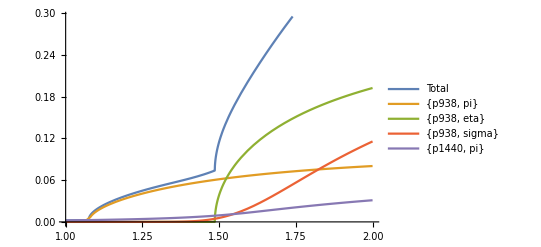

```mathematica
Block[{h=p1535},
Plot[Evaluate@Flatten@{
Γ[h,m],
Table[Γ[h,outs,m],{outs,decayProducts[h]}]
},{m,1.,2.},PlotLegends->Flatten@{"Total",ToString/@decayProducts[h]}]
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {1.48571}. NIntegrate obtained 6.5272 and 0.0000241659 for the integral and error estimates.

Calculating aN for p1535

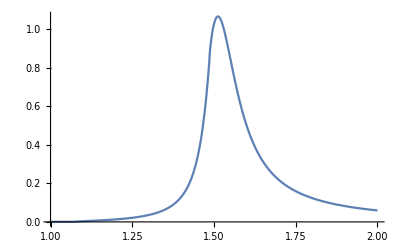

```mathematica
Block[{scale=a[p1535,m0[p1535]]/1.},
Plot[a[p1535,m]/scale,{m,1.,2.}]
]
```

```mathematica
a[p1535,m0[p1535]]/a[p1535,2.0]
```

16.8382